# Finding deflections

## α List

Choose ΩGW

```mathematica
Ωgw:=A f^3
```

α list

```mathematica
αlist={0.833333,0.116667,0.03,0.0104762,0.00442177,0.00212585,0.00112434,0.000639731,0.000385675,0.000243696}
```

{0.833333,0.116667,0.03,0.0104762,0.00442177,0.00212585,0.00112434,0.000639731,0.000385675,0.000243696}

Finding σ

```mathematica
σ=Ωgw/(f^2 (Integrate[f^-3 Ωgw,f]))
```

1

Finding θ RMS for E and B modes

```mathematica
θrms=(1/(4 π^2) Integrate[1/f(H/f)^2 Ωgw,f])^(1/2)
```

(√(A f H^2))/(2 π)

```mathematica
θElist=(θrms^2 gE σ αlist)^(1/2)
```

{0.145288 √(A f gE H^2),0.0543618 √(A f gE H^2),0.0275664 √(A f gE H^2),0.01629 √(A f gE H^2),0.0105832 √(A f gE H^2),0.00733815 √(A f gE H^2),0.00533665 √(A f gE H^2),0.00402549 √(A f gE H^2),0.00312558 √(A f gE H^2),0.00248453 √(A f gE H^2)}

```mathematica
θBlist=(θrms^2 gB σ αlist)^(1/2)
```

{0.145288 √(A f gB H^2),0.0543618 √(A f gB H^2),0.0275664 √(A f gB H^2),0.01629 √(A f gB H^2),0.0105832 √(A f gB H^2),0.00733815 √(A f gB H^2),0.00533665 √(A f gB H^2),0.00402549 √(A f gB H^2),0.00312558 √(A f gB H^2),0.00248453 √(A f gB H^2)}

## α Power law

α coeff power law

```mathematica
αlaw=32.34 l^-4.921
```

32.34/l^4.921

Finding θ E and B for Power law

```mathematica
θElaw=(θrms^2 gE σ αlaw)^(1/2)
```

0.905087 √((A f gE H^2)/l^4.921)

```mathematica
θBlaw=(θrms^2 gB σ αlaw)^(1/2)
```

0.905087 √((A f gB H^2)/l^4.921)

## Plotting α Power Law and α list

Defining variables to be able plot

```mathematica
gE:=1/2
gB:=1/2
```

```mathematica
H=N[UnitConvert[Quantity[70,("Kilometers"/("Megaparsecs"*"Seconds"))],1/"Seconds"]]
```

2.26855×10^-18 per second

```mathematica
A:=1*^-6
```

Period of observation Given by T

```mathematica
Tyears:=10
T=UnitConvert[Quantity[Tyears, "Years"],"Seconds"]
```

315360000 s

```mathematica
f=1/T
```

1/315360000 per second

Plot θElist

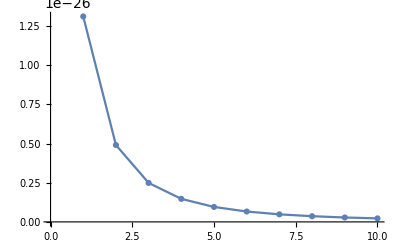

```mathematica
listplt=ListPlot[θElist, Joined->True,PlotMarkers->Automatic ]
```

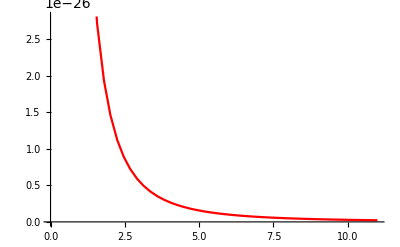

```mathematica
lawplt=Plot[θElaw, {l,0,11},PlotStyle->Red]
```

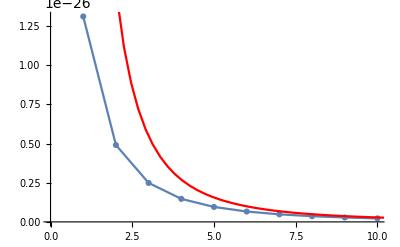

```mathematica
Show[listplt,lawplt]
```

Calculating deflection angle

```mathematica
δ=Integrate[1/f Sum[θElaw^2+θBlaw^2,{l,2,∞}],f]
```

Integrate::ilim: Invalid integration variable or limit(s) in 1/315360000.

∫(1.65515×10^-43 per second^2)ⅆ(1/315360000 per second)